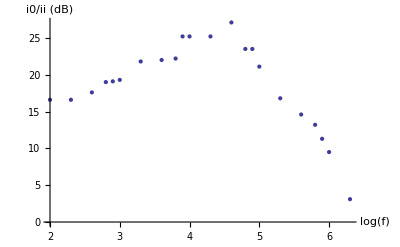

```mathematica
ListPlot[{{2.0,16.6},
{2.3,16.6},
{2.6,17.6},
{2.8,19.0},
{2.9,19.1},
{3.0,19.3},
{3.3,21.8},
{3.6,22.0},
{3.8,22.2},
{3.9,25.2},
{4.0,25.2},
{4.3,25.2},
{4.6,27.1},
{4.8,23.5},
{4.9,23.5},
{5.0,21.1},
{5.3,16.8},
{5.6,14.6},
{5.8,13.2},
{5.9,11.3},
{6.0,9.5},
{6.3,3.1}},AxesLabel->{"log(f)","i0/ii (dB)"}]
```

InterpolatingFunction[{{2.,6.3}},<>]

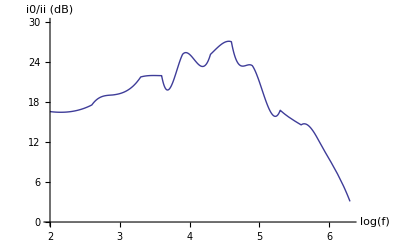

```mathematica
g=Interpolation[{{2.0,16.6},
{2.3,16.6},
{2.6,17.6},
{2.8,19.0},
{2.9,19.1},
{3.0,19.3},
{3.3,21.8},
{3.6,22.0},
{3.8,22.2},
{3.9,25.2},
{4.0,25.2},
{4.3,25.2},
{4.6,27.1},
{4.8,23.5},
{4.9,23.5},
{5.0,21.1},
{5.3,16.8},
{5.6,14.6},
{5.8,13.2},
{5.9,11.3},
{6.0,9.5},
{6.3,3.1}}]
Plot[g[x],{x,2,6.3},PlotRange->{{2,6.3},{0,30}},AxesLabel->{"log(f)","i0/ii (dB)"}]
```

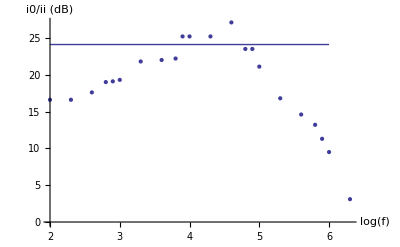

```mathematica
Show[ListPlot[{{2.0,16.6},
{2.3,16.6},
{2.6,17.6},
{2.8,19.0},
{2.9,19.1},
{3.0,19.3},
{3.3,21.8},
{3.6,22.0},
{3.8,22.2},
{3.9,25.2},
{4.0,25.2},
{4.3,25.2},
{4.6,27.1},
{4.8,23.5},
{4.9,23.5},
{5.0,21.1},
{5.3,16.8},
{5.6,14.6},
{5.8,13.2},
{5.9,11.3},
{6.0,9.5},
{6.3,3.1}},AxesLabel->{"log(f)","i0/ii (dB)"}], Plot[24.1,{x,2,6}]]
```